```mathematica
Quit
```

```mathematica
<<MaTeX`
texStyle={FontFamily->"Latin Modern Roman",FontSize->10};
```

```mathematica
percentTicks[plot_]:=Module[{xticks,yticks},{xticks,yticks}=(Ticks/.AbsoluteOptions[plot,Ticks]);
yticks=yticks/.{y_,lbl_,rest__}/;lbl≠"":>{y,ToString[y*100]<>"%",rest};
Show[plot,Ticks->{xticks,yticks}]]
```

## SIS model

NDSolve::ndcf: Repeated convergence test failure at t == 2.07891×10^152; unable to continue.

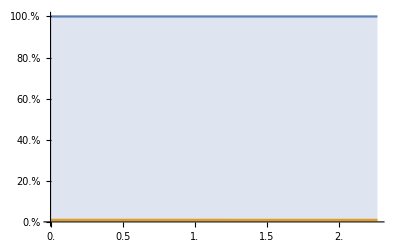

```mathematica
i0=0.01;
(*R0=10/(1-i0);*)γ=1;
β=10/10 γ;
s[t_]=1- i[t];
eqs={i'[t]==β i[t]s[t]-γ i[t]};
ic={i[0]==i0};
{sol}=NDSolve[eqs~Join~ic~Join~{WhenEvent[Log10@Abs[i'[t]]<-3,{"StopIntegration",tstop=t}]},{i[t]},{t,0,∞}];
(*Plot[Evaluate[{Callout[s[t],MaTeX["\\text{susceptibles}"]],Callout[i[t],MaTeX["\\text{infected}"]],Callout[s[t]+i[t],MaTeX["\\text{total}"]]}/.sol],{t,0,tstop},BaseStyle->texStyle]*)
plot1=percentTicks@Plot[Evaluate[{s[t]+i[t],i[t]}/.sol],{t,0,tstop},BaseStyle->texStyle,Filling->{1->{2},2->Axis,3->{1}},PlotRange->All,AxesLabel->{MaTeX["t"]},PlotLegends->Placed[SwatchLegend[MaTeX/@{"\\text{susceptibles}","\\text{infected}"}],Below],PlotLabel->MaTeX["\\gamma=1,~\\beta=1,~i_0=1\\% "](*,ImageSize->400*)]
```

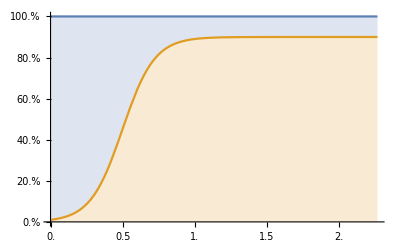

```mathematica
i0=0.01;
(*R0=10/(1-i0);*)γ=1;
β=100/10 γ;
s[t_]=1- i[t];
eqs={i'[t]==β i[t]s[t]-γ i[t]};
ic={i[0]==i0};
{sol}=NDSolve[eqs~Join~ic~Join~{WhenEvent[Log10@Abs[i'[t]]<-6,{"StopIntegration",tstop=t}]},{i[t]},{t,0,∞}];
(*Plot[Evaluate[{Callout[s[t],MaTeX["\\text{susceptibles}"]],Callout[i[t],MaTeX["\\text{infected}"]],Callout[s[t]+i[t],MaTeX["\\text{total}"]]}/.sol],{t,0,tstop},BaseStyle->texStyle]*)
plot2=percentTicks@Plot[Evaluate[{s[t]+i[t],i[t]}/.sol],{t,0,tstop},BaseStyle->texStyle,Filling->{1->{2},2->Axis,3->{1}},PlotRange->All,AxesLabel->{MaTeX["t"]},PlotLegends->Placed[SwatchLegend[MaTeX/@{"\\text{susceptibles}","\\text{infected}"}],Below],PlotLabel->MaTeX["\\gamma=1,~\\beta=10,~i_0=1\\% "](*,ImageSize->400*)]
```

```mathematica
plot=GraphicsRow[{plot1,plot2},ImageSize->400,Spacings->0,PlotLabel->MaTeX["\\text{SIS model of epidemiology}"]]
```

-Graphics-

```mathematica
Export["/Users/jerem/blog/images/posts_data/epidemiology-model/SIS.png",plot,ImageResolution->1000]
```

/Users/jerem/blog/images/posts_data/epidemiology-model/SIS.png

```mathematica
ClearAll[β,γ,i0]
DSolve[{i'[t]==(β-γ)i[t]-β i[t]^2},i[t],t]
```

{{i[t]→-(ⅇ^(t β+γ C[1]) (β-γ))/(ⅇ^(t γ+β C[1])-ⅇ^(t β+γ C[1]) β)}}

```mathematica
-(ⅇ^(t β+γ C[1]) (β-γ))/(ⅇ^(t γ+β C[1])-ⅇ^(t β+γ C[1]) β)/.C[1]->(-Log[i0/(-β+i0 β+γ)])/(β-γ)//FullSimplify
%/.β->α γ//FullSimplify
```

(i0 (-β+γ))/(-i0 β+ⅇ^(t (-β+γ)) ((-1+i0) β+γ))

(i0-i0 α)/(-i0 α+ⅇ^(t (γ-α γ)) (1+(-1+i0) α))

```mathematica
Collect[-i0 α+ⅇ^(t (γ-α γ)) (1+(-1+i0) α),ⅇ^(t (γ-α γ)),Simplify]
```

-i0 α+ⅇ^(t (γ-α γ)) (1+(-1+i0) α)

## SIR model

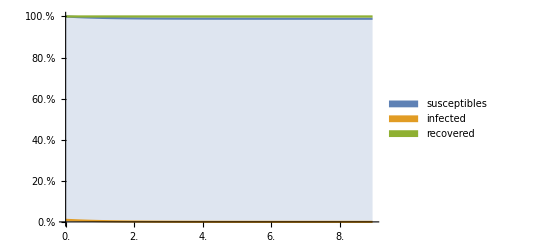

```mathematica
ClearAll[s,i,r]
i0=0.01;
R0=0.1/(1-i0);γ=1;
β=γ R0;
r[t_]=1-i[t]-s[t];
eqs={s'[t]==-β i[t]s[t],i'[t]==β i[t]s[t]-γ i[t]};
ic={s[0]==1-i0,i[0]==i0};
{sol}=NDSolve[eqs~Join~ic~Join~{WhenEvent[Log10@Abs[s'[t]]<-6.5,{"StopIntegration",tstop=t}]},{s[t],i[t]},{t,0,∞}];
(*Plot[Evaluate[{Callout[s[t],"susceptibles"],Callout[i[t],"infectés"],Callout[r[t],"immunisées"],Callout[s[t]+i[t]+r[t],"total"]}/.sol],{t,0,tstop},PlotStyle->{Automatic,Automatic,Automatic,Dashed}]*)
plot1=percentTicks@Plot[Evaluate[{s[t]+i[t],i[t],1}/.sol],{t,0,tstop},BaseStyle->texStyle,Filling->{1->{2},2->Axis,3->{1}},PlotRange->All,AxesLabel->{MaTeX["t"]},PlotLegends->Placed[SwatchLegend[{"susceptibles","infected","recovered"}],Below],PlotLabel->MaTeX["R_0=0.1/s_0,~\\gamma=1,~i_0=1\\% "]]
```

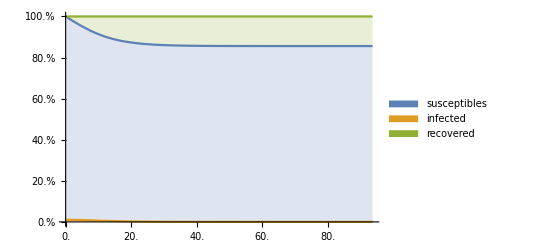

```mathematica
ClearAll[s,i,r]
i0=0.01;
R0=1/(1-i0);γ=1;
β=γ R0;
r[t_]=1-i[t]-s[t];
eqs={s'[t]==-β i[t]s[t],i'[t]==β i[t]s[t]-γ i[t]};
ic={s[0]==1-i0,i[0]==i0};
{sol}=NDSolve[eqs~Join~ic~Join~{WhenEvent[Log10@Abs[s'[t]]<-7,{"StopIntegration",tstop=t}]},{s[t],i[t]},{t,0,∞}];
(*Plot[Evaluate[{Callout[s[t],"susceptibles"],Callout[i[t],"infectés"],Callout[r[t],"immunisées"],Callout[s[t]+i[t]+r[t],"total"]}/.sol],{t,0,tstop},PlotStyle->{Automatic,Automatic,Automatic,Dashed}]*)
plot2=percentTicks@Plot[Evaluate[{s[t]+i[t],i[t],1}/.sol],{t,0,tstop},BaseStyle->texStyle,Filling->{1->{2},2->Axis,3->{1}},PlotRange->All,AxesLabel->{MaTeX["t"]},PlotLegends->Placed[SwatchLegend[{"susceptibles","infected","recovered"}],Below],PlotLabel->MaTeX["R_0=1/s_0,~\\gamma=1,~i_0=1\\% "]]
```

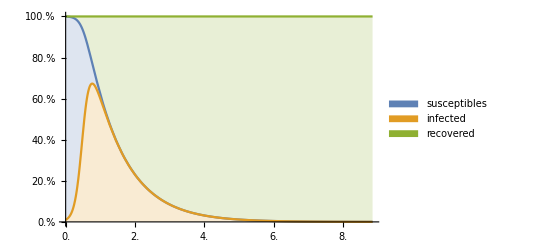

```mathematica
ClearAll[s,i,r]
i0=0.01;
R0=10/(1-i0);γ=1;
β=γ R0;
r[t_]=1-i[t]-s[t];
eqs={s'[t]==-β i[t]s[t],i'[t]==β i[t]s[t]-γ i[t]};
ic={s[0]==1-i0,i[0]==i0};
{sol}=NDSolve[eqs~Join~ic~Join~{WhenEvent[Log10@Abs[s'[t]]<-7,{"StopIntegration",tstop=t}]},{s[t],i[t]},{t,0,∞}];
(*Plot[Evaluate[{Callout[s[t],"susceptibles"],Callout[i[t],"infectés"],Callout[r[t],"immunisées"],Callout[s[t]+i[t]+r[t],"total"]}/.sol],{t,0,tstop},PlotStyle->{Automatic,Automatic,Automatic,Dashed}]*)
plot3=percentTicks@Plot[Evaluate[{s[t]+i[t],i[t],1}/.sol],{t,0,tstop},BaseStyle->texStyle,Filling->{1->{2},2->Axis,3->{1}},PlotRange->All,AxesLabel->{MaTeX["t"]},PlotLegends->Placed[SwatchLegend[{"susceptibles","infected","recovered"}],Below],PlotLabel->MaTeX["R_0=10/s_0,~\\gamma=1,~i_0=1\\% "]]
```

```mathematica
plot=GraphicsRow[{plot1,plot3},ImageSize->400,Spacings->0,PlotLabel->MaTeX["\\text{SIR model of epidemiology}"]]
```

-Graphics-

```mathematica
Export["/Users/jerem/blog/images/posts_data/epidemiology-model/SIR.png",plot,ImageResolution->1000]
```

/Users/jerem/blog/images/posts_data/epidemiology-model/SIR.png

```mathematica
ClearAll[s,i,r]
plots=Table[
i0=0.01;
R0=ii/(1-i0);γ=1;
β=γ R0;
r[t_]=1-i[t]-s[t];
eqs={s'[t]==-β i[t]s[t],i'[t]==β i[t]s[t]-γ i[t]};
ic={s[0]==1-i0,i[0]==i0};
{sol}=NDSolve[eqs~Join~ic~Join~{WhenEvent[Log10@Abs[s'[t]]<-7,{"StopIntegration",tstop=t}]},{s[t],i[t]},{t,0,∞}];
(*Plot[Evaluate[{Callout[s[t],"susceptibles"],Callout[i[t],"infectés"],Callout[r[t],"immunisées"],Callout[s[t]+i[t]+r[t],"total"]}/.sol],{t,0,tstop},PlotStyle->{Automatic,Automatic,Automatic,Dashed}]*)
percentTicks@Plot[Evaluate[{s[t]+i[t],i[t],1}/.sol],{t,0,10},BaseStyle->texStyle,Filling->{1->{2},2->Axis,3->{1}},PlotRange->All,AxesLabel->{MaTeX["t"]},PlotLegends->Placed[SwatchLegend[{"susceptibles","infected","recovered"}],Below],PlotLabel->MaTeX["R_0=" <>ToString[R0(1-i0)]<> "/s_0,~\\gamma=1,~i_0=1\\% "],ImageSize->400]
,{ii,10,1,-0.5}
];
```

```mathematica
Export["/Users/jerem/blog/images/posts_data/epidemiology-model/SIR.gif",plots,ImageResolution->500,"DisplayDurations"->0.5]
```

/Users/jerem/blog/images/posts_data/epidemiology-model/SIR.gif